```mathematica
Import["https://raw.githubusercontent.com/FeynCalc/feyncalc/master/install.m"];
InstallFeynCalc[]
```

$Aborted

```mathematica
T2=(GS[Subscript[p, 1]]-Subscript[m, ν])g(GS[Subscript[p, 1]']-Subscript[m, e])Conjugate[g] (GS[Subscript[p, 2]']+Subscript[m, Σ])Subscript[V, us] Subscript[g, W](GS[Subscript[p, 2]]+Subscript[m, n])Conjugate[Subscript[V, us]]Conjugate[Subscript[g, W]] GA[ν].(1-GA[5]) .GA[0].ConjugateTranspose[(1-GA[5])].ConjugateTranspose[GA[ν']].GA[0]. ( GA[μ]+(d-f)GA[μ,5]).GA[0].ConjugateTranspose[( GA[μ']+(d-f)GA[μ',5])].GA[0](( -I/((FV[Subscript[p, 1]-Subscript[p, 1]',λ])^2-Subscript[m, W]^2+Iϵ))(MetricTensor[μ,ν]-(FV[Subscript[p, 1]-Subscript[p, 1]',μ]FV[Subscript[p, 1]-Subscript[p, 1]',ν])/(FV[Subscript[p, 1]-Subscript[p, 1]',λ])^2)+(I(FV[Subscript[p, 1]-Subscript[p, 1]',μ]FV[Subscript[p, 1]-Subscript[p, 1]',ν]))/(Subscript[m, W]^2(FV[Subscript[p, 1]-Subscript[p, 1]',λ])^2))(( -I/((FV[Subscript[p, 1]-Subscript[p, 1]',λ])^2-Subscript[m, W]^2+Iϵ))(MetricTensor[μ',ν']-(FV[Subscript[p, 1]-Subscript[p, 1]',μ']FV[Subscript[p, 1]-Subscript[p, 1]',ν'])/(FV[Subscript[p, 1]-Subscript[p, 1]',λ])^2)+(I(FV[Subscript[p, 1]-Subscript[p, 1]',μ']FV[Subscript[p, 1]-Subscript[p, 1]',ν']))/(Subscript[m, W]^2(FV[Subscript[p, 1]-Subscript[p, 1]',λ])^2))
```

g Conjugate[g] g_W V_us Conjugate[(g_W)] Conjugate[(V_us)] (γ̄·(p̄)_2+m_n) (γ̄·(p̄)_1-m_ν) (γ̄·OverBar[p_1']-m_e) (γ̄·OverBar[p_2']+m_Σ) (γ̄)^ν.(1-(γ̄)^5).(γ̄)^0.ConjugateTranspose[(1-(γ̄)^5)].ConjugateTranspose[(γ̄)^ν'].(γ̄)^0.((γ̄)^μ+(d-f) (γ̄)^μ.(γ̄)^5).(γ̄)^0.ConjugateTranspose[((d-f) (γ̄)^μ'.(γ̄)^5+(γ̄)^μ')].(γ̄)^0 ((ⅈ ((p̄)_1-OverBar[p_1'])^μ ((p̄)_1-OverBar[p_1'])^ν)/(m_W^2 (((p̄)_1-OverBar[p_1'])^λ)^2)-(ⅈ ((ḡ)^μν-(((p̄)_1-OverBar[p_1'])^μ ((p̄)_1-OverBar[p_1'])^ν)/((((p̄)_1-OverBar[p_1'])^λ)^2)))/((((p̄)_1-OverBar[p_1'])^λ)^2+Iϵ-m_W^2)) ((ⅈ ((p̄)_1-OverBar[p_1'])^μ' ((p̄)_1-OverBar[p_1'])^ν')/(m_W^2 (((p̄)_1-OverBar[p_1'])^λ)^2)-(ⅈ ((ḡ)^(μ' ν')-(((p̄)_1-OverBar[p_1'])^μ' ((p̄)_1-OverBar[p_1'])^ν')/((((p̄)_1-OverBar[p_1'])^λ)^2)))/((((p̄)_1-OverBar[p_1'])^λ)^2+Iϵ-m_W^2))

```mathematica
T2//Tr
```

DiracTrick::failmsg: Error! DiracTrick has encountered a fatal problem and must abort the computation. The problem reads: Unexpanded nested DOTs detected!

$Aborted

```mathematica
GA[ν].(1-GA[5]) .GA[0].(1-ConjugateTranspose[GA[5]]).ConjugateTranspose[GA[ν']].GA[0]. ( GA[μ]+(d-f)GA[μ,5]).GA[0].( ConjugateTranspose[GA[μ']]+Conjugate[(d-f)]ConjugateTranspose[GA[5]].ConjugateTranspose[GA[μ']]).GA[0]
```

(γ̄)^ν.(1-(γ̄)^5).(γ̄)^0.(1-ConjugateTranspose[(γ̄)^5]).ConjugateTranspose[(γ̄)^ν'].(γ̄)^0.((γ̄)^μ+(d-f) (γ̄)^μ.(γ̄)^5).(γ̄)^0.((Conjugate[d]-Conjugate[f]) ConjugateTranspose[(γ̄)^5].ConjugateTranspose[(γ̄)^μ']+ConjugateTranspose[(γ̄)^μ']).(γ̄)^0

```mathematica
DiracTrace[GA[ν].(1-GA[5]) .GA[0].(1-GA[5]).GA[ν'].GA[0]. ( GA[μ]+(d-f)GA[μ,5]).GA[0].( GA[μ']+(d-f)GA[μ'].GA[5]).GA[0],DiracTraceEvaluate->False]
```

tr((γ̄)^ν.(1-(γ̄)^5).(γ̄)^0.(1-(γ̄)^5).(γ̄)^ν'.(γ̄)^0.((γ̄)^μ+(d-f) (γ̄)^μ.(γ̄)^5).(γ̄)^0.((γ̄)^μ'+(d-f) (γ̄)^μ'.(γ̄)^5).(γ̄)^0)

```mathematica
T2p=(GS[Subscript[p, 1]]-Subscript[m, ν])g(GS[Subscript[p, 1]']-Subscript[m, e])Conjugate[g] (GS[Subscript[p, 2]']+Subscript[m, Σ])Subscript[V, us] Subscript[g, W](GS[Subscript[p, 2]]+Subscript[m, n])Conjugate[Subscript[V, us]]Conjugate[Subscript[g, W]] GA[ν].(1-GA[5]).GA[ν'] .(1+GA[5]). ( GA[μ]+(d-f)GA[μ,5]).( GA[μ']+(d-f)GA[μ'].GA[5])(( -I/((FV[Subscript[p, 1]-Subscript[p, 1]',λ])^2-Subscript[m, W]^2+Iϵ))(MetricTensor[μ,ν]-(FV[Subscript[p, 1]-Subscript[p, 1]',μ]FV[Subscript[p, 1]-Subscript[p, 1]',ν])/(FV[Subscript[p, 1]-Subscript[p, 1]',λ])^2)+(I(FV[Subscript[p, 1]-Subscript[p, 1]',μ]FV[Subscript[p, 1]-Subscript[p, 1]',ν]))/(Subscript[m, W]^2(FV[Subscript[p, 1]-Subscript[p, 1]',λ])^2))(( -I/((FV[Subscript[p, 1]-Subscript[p, 1]',λ])^2-Subscript[m, W]^2+Iϵ))(MetricTensor[μ',ν']-(FV[Subscript[p, 1]-Subscript[p, 1]',μ']FV[Subscript[p, 1]-Subscript[p, 1]',ν'])/(FV[Subscript[p, 1]-Subscript[p, 1]',λ])^2)+(I(FV[Subscript[p, 1]-Subscript[p, 1]',μ']FV[Subscript[p, 1]-Subscript[p, 1]',ν']))/(Subscript[m, W]^2(FV[Subscript[p, 1]-Subscript[p, 1]',λ])^2))
```

g Conjugate[g] g_W V_us Conjugate[(g_W)] Conjugate[(V_us)] (γ̄·(p̄)_2+m_n) (γ̄·(p̄)_1-m_ν) (γ̄)^ν.(1-(γ̄)^5).(γ̄)^ν'.((γ̄)^5+1).((γ̄)^μ+(d-f) (γ̄)^μ.(γ̄)^5).((γ̄)^μ'+(d-f) (γ̄)^μ'.(γ̄)^5) (γ̄·OverBar[p_1']-m_e) (γ̄·OverBar[p_2']+m_Σ) ((ⅈ ((p̄)_1-OverBar[p_1'])^μ ((p̄)_1-OverBar[p_1'])^ν)/(m_W^2 (((p̄)_1-OverBar[p_1'])^λ)^2)-(ⅈ ((ḡ)^μν-(((p̄)_1-OverBar[p_1'])^μ ((p̄)_1-OverBar[p_1'])^ν)/((((p̄)_1-OverBar[p_1'])^λ)^2)))/((((p̄)_1-OverBar[p_1'])^λ)^2+Iϵ-m_W^2)) ((ⅈ ((p̄)_1-OverBar[p_1'])^μ' ((p̄)_1-OverBar[p_1'])^ν')/(m_W^2 (((p̄)_1-OverBar[p_1'])^λ)^2)-(ⅈ ((ḡ)^(μ' ν')-(((p̄)_1-OverBar[p_1'])^μ' ((p̄)_1-OverBar[p_1'])^ν')/((((p̄)_1-OverBar[p_1'])^λ)^2)))/((((p̄)_1-OverBar[p_1'])^λ)^2+Iϵ-m_W^2))

```mathematica
trace=T2p//Tr
```

(8 g Conjugate[g] (d-f-1) (d-f+1) m_e g_W m_ν m_n m_Σ V_us Conjugate[(g_W)] Conjugate[(V_us)] (OverBar[p_1']^2-2 ((p̄)_1·OverBar[p_1'])+((p̄)_1)^2)^2 (OverBar[p_1']^2-2 ((p̄)_1·OverBar[p_1'])+((p̄)_1)^2+Iϵ)^2)/(m_W^4 (((p̄)_1-OverBar[p_1'])^λ)^4 (OverBar[p_1']^2-2 ((p̄)_1·OverBar[p_1'])+((p̄)_1)^2+Iϵ-m_W^2)^2)+(32 g Conjugate[g] (d-f-1) (d-f+1) m_e g_W m_ν m_n m_Σ V_us Conjugate[(g_W)] Conjugate[(V_us)] (OverBar[p_1']^2-2 ((p̄)_1·OverBar[p_1'])+((p̄)_1)^2) (OverBar[p_1']^2-2 ((p̄)_1·OverBar[p_1'])+((p̄)_1)^2+Iϵ))/(m_W^2 (((p̄)_1-OverBar[p_1'])^λ)^2 (OverBar[p_1']^2-2 ((p̄)_1·OverBar[p_1'])+((p̄)_1)^2+Iϵ-m_W^2)^2)-(64 g Conjugate[g] (d-f-1) (d-f+1) m_e g_W m_ν m_n m_Σ V_us Conjugate[(g_W)] Conjugate[(V_us)])/((OverBar[p_1']^2-2 ((p̄)_1·OverBar[p_1'])+((p̄)_1)^2+Iϵ-m_W^2)^2)

```mathematica
trace//Simplify
```

(8 g Conjugate[g] (d-f-1) (d-f+1) m_e g_W m_ν m_n m_Σ V_us Conjugate[(g_W)] Conjugate[(V_us)] (((OverBar[p_1']^2-2 ((p̄)_1·OverBar[p_1'])+((p̄)_1)^2)^2 (OverBar[p_1']^2-2 ((p̄)_1·OverBar[p_1'])+((p̄)_1)^2+Iϵ)^2)/(m_W^4 (((p̄)_1-OverBar[p_1'])^λ)^4)+(4 (OverBar[p_1']^2-2 ((p̄)_1·OverBar[p_1'])+((p̄)_1)^2) (OverBar[p_1']^2-2 ((p̄)_1·OverBar[p_1'])+((p̄)_1)^2+Iϵ))/(m_W^2 (((p̄)_1-OverBar[p_1'])^λ)^2)-8))/((OverBar[p_1']^2-2 ((p̄)_1·OverBar[p_1'])+((p̄)_1)^2+Iϵ-m_W^2)^2)

```mathematica
T2pp=g Conjugate[g] Subscript[V, us] Subscript[g, W] Conjugate[Subscript[V, us]]Conjugate[Subscript[g, W]] TR[(GS[Subscript[p, 1]]-Subscript[m, ν]).GA[ν].(1-GA[5]).(GS[Subscript[p, 1]']-Subscript[m, e]).GA[ν'] .(1-GA[5])]TR[(GS[Subscript[p, 2]']+Subscript[m, Σ]). ( GA[μ]+(d-f)GA[μ,5]).(GS[Subscript[p, 2]]+Subscript[m, n]).( GA[μ']+(d-f)GA[μ'].GA[5])](( -I/((FV[Subscript[p, 1]-Subscript[p, 1]',λ])^2-Subscript[m, W]^2+Iϵ))(MetricTensor[μ,ν]))(( -I/((FV[Subscript[p, 1]-Subscript[p, 1]',λ])^2-Subscript[m, W]^2+Iϵ))(MetricTensor[μ',ν']))//Calc//Simplify
```

-(64 g Conjugate[g] g_W V_us Conjugate[(g_W)] Conjugate[(V_us)] ((d-f+1) ((d-f-1) m_n m_Σ ((p̄)_1·OverBar[p_1'])+(d-f+1) ((p̄)_1·(p̄)_2) (OverBar[p_1']·OverBar[p_2']))+(-d+f+1)^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1'])))/((OverBar[p_1']^2-2 ((p̄)_1·OverBar[p_1'])+((p̄)_1)^2+Iϵ-m_W^2)^2)

### Calculate cross section

First, calculate the square of the scattering amplitude, i.e. | 𝒯|^2.

```mathematica
trace=g Conjugate[g] Subscript[V, us] Subscript[g, W] Conjugate[Subscript[V, us]]Conjugate[Subscript[g, W]] TR[(GS[Subscript[p, 1]]-Subscript[m, ν]).GA[ν].(1-GA[5]).(GS[Subscript[p, 1]']-Subscript[m, e]).GA[ν'] .(1-GA[5])]TR[(GS[Subscript[p, 2]']+Subscript[m, Σ]). ( GA[μ]+(d-f)GA[μ,5]).(GS[Subscript[p, 2]]+Subscript[m, n]).( GA[μ']+(d-f)GA[μ'].GA[5])](( -I SFAD[{Subscript[p, 1]-Subscript[p, 1]',Subscript[m, W]^2}])(MetricTensor[μ,ν]-(FV[Subscript[p, 1]-Subscript[p, 1]',μ]FV[Subscript[p, 1]-Subscript[p, 1]',ν])/Subscript[m, W]^2))(( -I SFAD[{Subscript[p, 1]-Subscript[p, 1]',Subscript[m, W]^2}])(MetricTensor[μ',ν']-(FV[Subscript[p, 1]-Subscript[p, 1]',μ']FV[Subscript[p, 1]-Subscript[p, 1]',ν'])/Subscript[m, W]^2))
```

-32 g Conjugate[g] g_W V_us Conjugate[(g_W)] Conjugate[(V_us)] (-(ḡ)^(ν ν') ((p̄)_1·OverBar[p_1'])+OverBar[p_1']^ν ((p̄)_1)^ν'+((p̄)_1)^ν OverBar[p_1']^ν'-ⅈ (ϵ̄)^(ν ν'(p̄)_1 OverBar[p_1'])) ((ḡ)^μν-(((p̄)_1-OverBar[p_1'])^μ ((p̄)_1-OverBar[p_1'])^ν)/m_W^2) ((ḡ)^(μ' ν')-(((p̄)_1-OverBar[p_1'])^μ' ((p̄)_1-OverBar[p_1'])^ν')/m_W^2) (1/((p_1-p_1')^2-m_W^2+ⅈ η))^2 (-d^2 m_n m_Σ (ḡ)^(μ μ')-d^2 (ḡ)^(μ μ') ((p̄)_2·OverBar[p_2'])+d^2 OverBar[p_2']^μ ((p̄)_2)^μ'+d^2 ((p̄)_2)^μ OverBar[p_2']^μ'+2 d f m_n m_Σ (ḡ)^(μ μ')+2 d f (ḡ)^(μ μ') ((p̄)_2·OverBar[p_2'])-2 d f OverBar[p_2']^μ ((p̄)_2)^μ'-2 d f ((p̄)_2)^μ OverBar[p_2']^μ'-2 ⅈ d (ϵ̄)^(μ μ'(p̄)_2 OverBar[p_2'])-f^2 m_n m_Σ (ḡ)^(μ μ')-f^2 (ḡ)^(μ μ') ((p̄)_2·OverBar[p_2'])+f^2 OverBar[p_2']^μ ((p̄)_2)^μ'+f^2 ((p̄)_2)^μ OverBar[p_2']^μ'+2 ⅈ f (ϵ̄)^(μ μ'(p̄)_2 OverBar[p_2'])+m_n m_Σ (ḡ)^(μ μ')-(ḡ)^(μ μ') ((p̄)_2·OverBar[p_2'])+OverBar[p_2']^μ ((p̄)_2)^μ'+((p̄)_2)^μ OverBar[p_2']^μ')

```mathematica
sa=trace//Calc//Simplify
```

1/(((p_1-p_1')^2-m_W^2+ⅈ η)^2 m_W^4)32 g Conjugate[g] Conjugate[(g_W)] Conjugate[(V_us)] g_W (-2 d^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4-2 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+4 d ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+4 d f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4-4 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4-2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4-2 d^2 ((p̄)_1·OverBar[p_1']) m_n m_Σ m_W^4-2 f^2 ((p̄)_1·OverBar[p_1']) m_n m_Σ m_W^4+4 d f ((p̄)_1·OverBar[p_1']) m_n m_Σ m_W^4+2 ((p̄)_1·OverBar[p_1']) m_n m_Σ m_W^4+2 d^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2+2 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2-4 d f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2+2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2-2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2-2 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+4 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2-2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2-2 d^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_Σ m_W^2-2 f^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_Σ m_W^2+4 d f ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_Σ m_W^2+2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_Σ m_W^2+d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4+f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-2 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4+((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4+2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2+2 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-4 d f ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2+2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-2 d^2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2-2 f^2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2+4 d f ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2-2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2-2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-2 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+4 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-2 ((p̄)_1·(p̄)_2) ((2 (d^2-2 f d+f^2+1) ((p̄)_1·OverBar[p_2']) OverBar[p_1']^2+(OverBar[p_1']·OverBar[p_2']) ((d-f+1)^2 m_W^2-(d^2-2 f d+f^2+1) OverBar[p_1']^2)) m_W^2+(d^2-2 f d+f^2+1) ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 ((p̄)_1·OverBar[p_2']-OverBar[p_1']·OverBar[p_2']))+d^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_Σ+f^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_Σ-2 d f ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_Σ-((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_Σ-2 d^2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_Σ-2 f^2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_Σ+4 d f ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_Σ+2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_Σ+((p̄)_1)^4 ((p̄)_1·OverBar[p_1']-2 OverBar[p_1']^2) ((d^2-2 f d+f^2+1) ((p̄)_2·OverBar[p_2'])+(d^2-2 f d+f^2-1) m_n m_Σ)-2 ((p̄)_1)^2 (((p̄)_2·OverBar[p_2']) OverBar[p_1']^4 d^2-((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2 d^2-2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2 d^2+2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2 d^2+2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 d^2-2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2']) d^2-2 OverBar[p_1']^2 m_n m_W^2 m_Σ d^2+OverBar[p_1']^4 m_n m_Σ d^2-2 f ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4 d+2 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2 d+4 f ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2 d-4 f ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2 d-4 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 d+4 f ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2']) d+4 f OverBar[p_1']^2 m_n m_W^2 m_Σ d-2 f OverBar[p_1']^4 m_n m_Σ d+f^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4+((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2-((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2-2 f^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2-2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+2 f^2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2+2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2+2 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2+2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-2 f^2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+(d^2-2 f d+f^2+1) ((p̄)_1·(p̄)_2) (-2 ((p̄)_1·OverBar[p_2']) OverBar[p_1']^2+((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']-OverBar[p_1']·OverBar[p_2'])+(OverBar[p_1']·OverBar[p_2']) (2 OverBar[p_1']^2-m_W^2))-2 f^2 OverBar[p_1']^2 m_n m_W^2 m_Σ+2 OverBar[p_1']^2 m_n m_W^2 m_Σ+f^2 OverBar[p_1']^4 m_n m_Σ-OverBar[p_1']^4 m_n m_Σ+((p̄)_1·OverBar[p_1'])^2 ((d^2-2 f d+f^2+1) ((p̄)_2·OverBar[p_2'])+(d^2-2 f d+f^2-1) m_n m_Σ)+((p̄)_1·OverBar[p_1']) (((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) d^2+m_n m_W^2 m_Σ d^2-3 OverBar[p_1']^2 m_n m_Σ d^2-2 f ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) d-2 f m_n m_W^2 m_Σ d+6 f OverBar[p_1']^2 m_n m_Σ d-(d^2-2 f d+f^2+1) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1'])+f^2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2'])+((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2'])-(d^2-2 f d+f^2+1) ((p̄)_2·OverBar[p_2']) (3 OverBar[p_1']^2-m_W^2)+f^2 m_n m_W^2 m_Σ-m_n m_W^2 m_Σ-3 f^2 OverBar[p_1']^2 m_n m_Σ+3 OverBar[p_1']^2 m_n m_Σ))) V_us

Then, calculate the cross section dσ/dt=1/(64πs)1/(|p_(1_CM)|^2)(|𝒯|)^2

```mathematica
cs=1/(64π s) s/(Pair[Momentum[Subscript[p, 1]],Momentum[Subscript[p, 2]]]^2-Subscript[m, ν]^2 Subscript[m, n]^2)sa
```

(g Conjugate[g] Conjugate[(g_W)] Conjugate[(V_us)] g_W (-2 d^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4-2 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+4 d ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4+4 d f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4-4 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4-2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^4-2 d^2 ((p̄)_1·OverBar[p_1']) m_n m_Σ m_W^4-2 f^2 ((p̄)_1·OverBar[p_1']) m_n m_Σ m_W^4+4 d f ((p̄)_1·OverBar[p_1']) m_n m_Σ m_W^4+2 ((p̄)_1·OverBar[p_1']) m_n m_Σ m_W^4+2 d^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2+2 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2-4 d f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2+2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 m_W^2-2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2-2 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+4 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2-2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2-2 d^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_Σ m_W^2-2 f^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_Σ m_W^2+4 d f ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_Σ m_W^2+2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 m_n m_Σ m_W^2+d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4+f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-2 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4+((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4+2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2+2 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-4 d f ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2+2 ((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-2 d^2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2-2 f^2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2+4 d f ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2-2 ((p̄)_1·OverBar[p_1'])^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2-2 d^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-2 f^2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+4 d f ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-2 ((p̄)_1·OverBar[p_1']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-2 ((p̄)_1·(p̄)_2) ((2 (d^2-2 f d+f^2+1) ((p̄)_1·OverBar[p_2']) OverBar[p_1']^2+(OverBar[p_1']·OverBar[p_2']) ((d-f+1)^2 m_W^2-(d^2-2 f d+f^2+1) OverBar[p_1']^2)) m_W^2+(d^2-2 f d+f^2+1) ((p̄)_1·OverBar[p_1']) OverBar[p_1']^2 ((p̄)_1·OverBar[p_2']-OverBar[p_1']·OverBar[p_2']))+d^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_Σ+f^2 ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_Σ-2 d f ((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_Σ-((p̄)_1·OverBar[p_1']) OverBar[p_1']^4 m_n m_Σ-2 d^2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_Σ-2 f^2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_Σ+4 d f ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_Σ+2 ((p̄)_1·OverBar[p_1'])^2 OverBar[p_1']^2 m_n m_Σ+((p̄)_1)^4 ((p̄)_1·OverBar[p_1']-2 OverBar[p_1']^2) ((d^2-2 f d+f^2+1) ((p̄)_2·OverBar[p_2'])+(d^2-2 f d+f^2-1) m_n m_Σ)-2 ((p̄)_1)^2 (((p̄)_2·OverBar[p_2']) OverBar[p_1']^4 d^2-((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2 d^2-2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2 d^2+2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2 d^2+2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 d^2-2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2']) d^2-2 OverBar[p_1']^2 m_n m_W^2 m_Σ d^2+OverBar[p_1']^4 m_n m_Σ d^2-2 f ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4 d+2 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2 d+4 f ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2 d-4 f ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2 d-4 f ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 d+4 f ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2']) d+4 f OverBar[p_1']^2 m_n m_W^2 m_Σ d-2 f OverBar[p_1']^4 m_n m_Σ d+f^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^4+((p̄)_2·OverBar[p_2']) OverBar[p_1']^4-f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2-((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) m_W^2-2 f^2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2-2 ((p̄)_2·OverBar[p_2']) OverBar[p_1']^2 m_W^2+2 f^2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2+2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) m_W^2+2 f^2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2+2 ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2-2 f^2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])-2 ((p̄)_2·OverBar[p_1']) OverBar[p_1']^2 (OverBar[p_1']·OverBar[p_2'])+(d^2-2 f d+f^2+1) ((p̄)_1·(p̄)_2) (-2 ((p̄)_1·OverBar[p_2']) OverBar[p_1']^2+((p̄)_1·OverBar[p_1']) ((p̄)_1·OverBar[p_2']-OverBar[p_1']·OverBar[p_2'])+(OverBar[p_1']·OverBar[p_2']) (2 OverBar[p_1']^2-m_W^2))-2 f^2 OverBar[p_1']^2 m_n m_W^2 m_Σ+2 OverBar[p_1']^2 m_n m_W^2 m_Σ+f^2 OverBar[p_1']^4 m_n m_Σ-OverBar[p_1']^4 m_n m_Σ+((p̄)_1·OverBar[p_1'])^2 ((d^2-2 f d+f^2+1) ((p̄)_2·OverBar[p_2'])+(d^2-2 f d+f^2-1) m_n m_Σ)+((p̄)_1·OverBar[p_1']) (((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) d^2+m_n m_W^2 m_Σ d^2-3 OverBar[p_1']^2 m_n m_Σ d^2-2 f ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2']) d-2 f m_n m_W^2 m_Σ d+6 f OverBar[p_1']^2 m_n m_Σ d-(d^2-2 f d+f^2+1) ((p̄)_1·OverBar[p_2']) ((p̄)_2·OverBar[p_1'])+f^2 ((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2'])+((p̄)_2·OverBar[p_1']) (OverBar[p_1']·OverBar[p_2'])-(d^2-2 f d+f^2+1) ((p̄)_2·OverBar[p_2']) (3 OverBar[p_1']^2-m_W^2)+f^2 m_n m_W^2 m_Σ-m_n m_W^2 m_Σ-3 f^2 OverBar[p_1']^2 m_n m_Σ+3 OverBar[p_1']^2 m_n m_Σ))) V_us)/(2 π ((p_1-p_1')^2-m_W^2+ⅈ η)^2 m_W^4 (((p̄)_1·(p̄)_2)^2-m_n^2 m_ν^2))

Substitute the Mandelstam variables.

```mathematica
csmandelstam=cs/.{Pair[Momentum[Subscript[p, 1]],Momentum[Subscript[p, 1]']]->(Subscript[m, ν]^2+Subscript[m, e]^2-t)/2,Pair[Momentum[Subscript[p, 1]],Momentum[Subscript[p, 2]]]->(s-Subscript[m, ν]^2-Subscript[m, n]^2)/2,Pair[Momentum[Subscript[p, 1]],Momentum[Subscript[p, 2]']]->(s+t-Subscript[m, n]^2-Subscript[m, e]^2)/2,Pair[Momentum[Subscript[p, 1]'],Momentum[Subscript[p, 2]]]->(s+t-Subscript[m, ν]^2-Subscript[m, Σ]^2)/2,Pair[Momentum[Subscript[p, 1]'],Momentum[Subscript[p, 2]']]->(s-Subscript[m, e]^2-Subscript[m, Σ]^2)/2,Pair[Momentum[Subscript[p, 2]],Momentum[Subscript[p, 2]']]->(Subscript[m, n]^2+Subscript[m, Σ]^2-t)/2, Pair[Momentum[Subscript[p, 1]],Momentum[Subscript[p, 1]]]->Subscript[m, ν]^2, Pair[Momentum[Subscript[p, 1]'],Momentum[Subscript[p, 1]']]->Subscript[m, e]^2,FeynAmpDenominator[StandardPropagatorDenominator[Momentum[Subscript[p, 1],D]-Momentum[Subscript[p, 1]',D],0,-Subscript[m, W]^2,{1,1}],StandardPropagatorDenominator[Momentum[Subscript[p, 1],D]-Momentum[Subscript[p, 1]',D],0,-Subscript[m, W]^2,{1,1}]]->1/((t-Subscript[m, W]^2)^2)}//Simplify
```

-((g Conjugate[g] Conjugate[(g_W)] Conjugate[(V_us)] g_W (((d^2-2 f d+f^2+1) m_n^4-(d^2-2 f d+f^2+1) (-4 m_W^2+2 m_Σ^2+t) m_n^2-2 (d^2-2 f d+f^2-1) (t-2 m_W^2) m_Σ m_n+(d^2-2 f d+f^2+1) m_Σ^2 (m_Σ^2-t)) m_e^4+(-((d^2-2 f d+f^2+1) (-4 m_W^2+2 m_ν^2+t) m_n^4)+(2 (d-f+1)^2 m_W^4-4 (d^2-2 f d+f^2+1) (m_ν^2+m_Σ^2+s+t) m_W^2+(d^2-2 f d+f^2+1) (2 m_ν^2+t) (2 m_Σ^2+t)) m_n^2+2 (d^2-2 f d+f^2-1) (2 m_W^4-2 (2 m_ν^2+t) m_W^2+t (2 m_ν^2+t)) m_Σ m_n-4 d^2 s m_W^4-4 f^2 s m_W^4+8 d f s m_W^4-4 s m_W^4-2 d^2 t m_W^4-2 f^2 t m_W^4+4 d t m_W^4+4 d f t m_W^4-4 f t m_W^4-2 t m_W^4-2 d^2 m_ν^2 m_Σ^4-2 f^2 m_ν^2 m_Σ^4+4 d f m_ν^2 m_Σ^4-2 m_ν^2 m_Σ^4-d^2 t m_Σ^4-f^2 t m_Σ^4+2 d f t m_Σ^4-t m_Σ^4+4 d^2 m_W^4 m_ν^2+4 f^2 m_W^4 m_ν^2-8 d f m_W^4 m_ν^2+4 m_W^4 m_ν^2+2 d^2 m_W^4 m_Σ^2+2 f^2 m_W^4 m_Σ^2-4 d m_W^4 m_Σ^2-4 d f m_W^4 m_Σ^2+4 f m_W^4 m_Σ^2+2 m_W^4 m_Σ^2+d^2 t^2 m_Σ^2+f^2 t^2 m_Σ^2-2 d f t^2 m_Σ^2+t^2 m_Σ^2+4 d^2 s m_W^2 m_Σ^2+4 f^2 s m_W^2 m_Σ^2-8 d f s m_W^2 m_Σ^2+4 s m_W^2 m_Σ^2-4 d^2 m_W^2 m_ν^2 m_Σ^2-4 f^2 m_W^2 m_ν^2 m_Σ^2+8 d f m_W^2 m_ν^2 m_Σ^2-4 m_W^2 m_ν^2 m_Σ^2+2 d^2 t m_ν^2 m_Σ^2+2 f^2 t m_ν^2 m_Σ^2-4 d f t m_ν^2 m_Σ^2+2 t m_ν^2 m_Σ^2) m_e^2+4 m_W^2 m_ν^2 ((d^2-2 f d+f^2+1) (s-m_Σ^2) m_n^2-(d^2-2 f d+f^2-1) (t-m_ν^2) m_Σ m_n+(d^2-2 f d+f^2+1) m_Σ^2 (m_ν^2+m_Σ^2-s-t))+2 m_W^4 (2 s^2 d^2+t^2 d^2-2 s m_Σ^2 d^2-t m_Σ^2 d^2+2 s t d^2-4 f s^2 d-2 f t^2 d-2 t^2 d+4 f s m_Σ^2 d+2 f t m_Σ^2 d+2 t m_Σ^2 d-4 f s t d-4 s t d+2 f^2 s^2+2 s^2+f^2 t^2+2 f t^2+t^2-2 f^2 s m_Σ^2-2 s m_Σ^2-f^2 t m_Σ^2-2 f t m_Σ^2-t m_Σ^2+2 f^2 s t+4 f s t+2 s t-2 (d^2-2 f d+f^2-1) m_n (t-m_ν^2) m_Σ-m_ν^2 (t (-d+f+1)^2-(d-f+1)^2 m_Σ^2+2 (d^2-2 f d+f^2+1) s)+m_n^2 (-2 s d^2-t d^2+4 f s d+2 f t d+2 t d+(-d+f+1)^2 m_ν^2+2 (d^2-2 f d+f^2+1) m_Σ^2-2 f^2 s-2 s-f^2 t-2 f t-t))+m_ν^2 (-((d^2-2 f d+f^2+1) (t-m_ν^2) m_n^4)+(d^2-2 f d+f^2+1) (t-m_ν^2) (2 m_Σ^2+t) m_n^2+2 (d^2-2 f d+f^2-1) t (t-m_ν^2) m_Σ m_n+(d^2-2 f d+f^2+1) m_Σ^2 ((m_Σ^2-t) m_ν^2+t (t-m_Σ^2)))) V_us)/(2 π m_W^4 (t-m_W^2)^2 (m_n^4-2 (m_ν^2+s) m_n^2+(s-m_ν^2)^2)))

Define the limits of integration.

```mathematica
t0=((Subscript[m, ν]^2-Subscript[m, e]^2-Subscript[m, n]^2+Subscript[m, Σ]^2)/(2Sqrt[s]))^2-(Sqrt[((s+Subscript[m, ν]^2-Subscript[m, n]^2)/(2Sqrt[s]))^2-Subscript[m, ν]^2]-Sqrt[((s+Subscript[m, e]^2-Subscript[m, Σ]^2)/(2Sqrt[s]))^2-Subscript[m, e]^2])^2/.{Subscript[m, W]->80.377,Subscript[m, e]->0.51100*10^{-3},Subscript[m, ν]->0,Subscript[m, Σ]->1197.4*10^{-3},Subscript[m, n]->939.57*10^{-3}};
t1=((Subscript[m, ν]^2-Subscript[m, e]^2-Subscript[m, n]^2+Subscript[m, Σ]^2)/(2Sqrt[s]))^2-(Sqrt[((s+Subscript[m, ν]^2-Subscript[m, n]^2)/(2Sqrt[s]))^2-Subscript[m, ν]^2]+Sqrt[((s+Subscript[m, e]^2-Subscript[m, Σ]^2)/(2Sqrt[s]))^2-Subscript[m, e]^2])^2/.{Subscript[m, W]->80.377,Subscript[m, e]->0.51100*10^{-3},Subscript[m, ν]->0,Subscript[m, Σ]->1197.4*10^{-3},Subscript[m, n]->939.57*10^{-3}};
t0f[s_]:=Evaluate[t0[[1]]]

t1f[s_]:=Evaluate[t1[[1]]]
```

Substitute values of constants and masses in GeV

```mathematica
csmandelstamsubstitued=csmandelstam/.{Subscript[m, W]->80.377,Subscript[m, e]->0.51100*10^{-3},Subscript[m, ν]->0,Subscript[m, Σ]->1197.4*10^{-3},Subscript[m, n]->939.57*10^{-3},Subscript[V, us]->0.22430,d->0.80,f->0.46,g->0.652,Subscript[g, W]->0.652};
csmandelstamsubstituedexp=csmandelstamsubstitued[[1]]
crf[s_]:=Evaluate[csmandelstamsubstituedexp];
```

-1/((s^2-1.76558 s+0.779321) (t-6460.46)^2)3.4669×10^-11 (6.81842×10^-14 (1.59951 (1.43377-t)-0.984843 (t-25839.)+1.98997 (t-12920.9)+0.869411)+8.34751×10^7 (2.2312 s^2+0.8712 s t+0.882792 (-2.2312 s-0.4356 t+3.19902)-3.19902 s+0.4356 t^2+1.36542 t)+2.61121×10^-7 (0.882792 (-28829.2 (s+t+1.43377)+1.1156 t (t+2.86753)+1.49888×10^8)-1.86208×10^8 s+1.59951 t^2-1.98997 (t^2-12920.9 t+8.34751×10^7)-3.63618×10^7 t-0.869411 (t-25841.8)+5.21343×10^7)+0.)

Integrate the cross section

```mathematica
sigma[s_?NumericQ]:=NIntegrate[crf[s],{t,t0f[s],t1f[s]}]
```

Defining the minimum and maximum energy
min: ((m_e+m_Σ))^2
max: m_n(m_n+2)

```mathematica
lower=(0.51100*10^{-3}+1197.4*10^{-3})^2;
upper=939.57*10^{-3}(939.57*10^{-3}+2);
lower[[1]]
upper[[1]]
```

1.43499

2.76193

```mathematica
t0f[lower[[1]]]
t0f[upper[[1]]]
t1f[lower[[1]]]
t1f[upper[[1]]]
```

-0.000235294+1.96859×10^-10 ⅈ

-1.08323×10^-7

-0.000235294-1.96859×10^-10 ⅈ

-0.903645

Plot the cross section in terms of energy

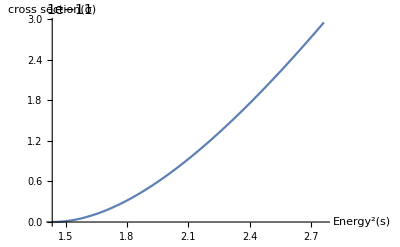

```mathematica
Plot[0.4*sigma[s],{s,lower[[1]],upper[[1]]}, Axes->True,AxesLabel->{(Energy^2)[s],cross section[σ]}]
```

lower m_n+m_Σ, upper m_n(m_n+2)

{0.000511}

```mathematica
rules=Thread[Rule[{x,y,z},{1,2,3}]]

x^2+y^2+z^3+x*z/.{x->1,y->2,z->3}
```

{x→1,y→2,z→3}

35

```mathematica
crosssection=1/(64π s) s/(Pair[Momentum[Subscript[p, 1]],Momentum[Subscript[p, 2]]]^2-Subscript[m, ν]^2 Subscript[m, n]^2)csmandelstam//Simplify
```

-1/(8 π m_W^4 (t-m_W^2)^2 (((p̄)_1·(p̄)_2)^2-m_n^2 m_ν^2))g Conjugate[g] Conjugate[(g_W)] Conjugate[(V_us)] g_W (((d^2-2 f d+f^2+1) m_n^4-(d^2-2 f d+f^2+1) (-4 m_W^2+2 m_Σ^2+t) m_n^2-2 (d^2-2 f d+f^2-1) (t-2 m_W^2) m_Σ m_n+(d^2-2 f d+f^2+1) m_Σ^2 (m_Σ^2-t)) m_e^4+(-((d^2-2 f d+f^2+1) (-4 m_W^2+2 m_ν^2+t) m_n^4)+(2 (d-f+1)^2 m_W^4-4 (d^2-2 f d+f^2+1) (m_ν^2+m_Σ^2+s+t) m_W^2+(d^2-2 f d+f^2+1) (2 m_ν^2+t) (2 m_Σ^2+t)) m_n^2+2 (d^2-2 f d+f^2-1) (2 m_W^4-2 (2 m_ν^2+t) m_W^2+t (2 m_ν^2+t)) m_Σ m_n-4 d^2 s m_W^4-4 f^2 s m_W^4+8 d f s m_W^4-4 s m_W^4-2 d^2 t m_W^4-2 f^2 t m_W^4+4 d t m_W^4+4 d f t m_W^4-4 f t m_W^4-2 t m_W^4-2 d^2 m_ν^2 m_Σ^4-2 f^2 m_ν^2 m_Σ^4+4 d f m_ν^2 m_Σ^4-2 m_ν^2 m_Σ^4-d^2 t m_Σ^4-f^2 t m_Σ^4+2 d f t m_Σ^4-t m_Σ^4+4 d^2 m_W^4 m_ν^2+4 f^2 m_W^4 m_ν^2-8 d f m_W^4 m_ν^2+4 m_W^4 m_ν^2+2 d^2 m_W^4 m_Σ^2+2 f^2 m_W^4 m_Σ^2-4 d m_W^4 m_Σ^2-4 d f m_W^4 m_Σ^2+4 f m_W^4 m_Σ^2+2 m_W^4 m_Σ^2+d^2 t^2 m_Σ^2+f^2 t^2 m_Σ^2-2 d f t^2 m_Σ^2+t^2 m_Σ^2+4 d^2 s m_W^2 m_Σ^2+4 f^2 s m_W^2 m_Σ^2-8 d f s m_W^2 m_Σ^2+4 s m_W^2 m_Σ^2-4 d^2 m_W^2 m_ν^2 m_Σ^2-4 f^2 m_W^2 m_ν^2 m_Σ^2+8 d f m_W^2 m_ν^2 m_Σ^2-4 m_W^2 m_ν^2 m_Σ^2+2 d^2 t m_ν^2 m_Σ^2+2 f^2 t m_ν^2 m_Σ^2-4 d f t m_ν^2 m_Σ^2+2 t m_ν^2 m_Σ^2) m_e^2+4 m_W^2 m_ν^2 ((d^2-2 f d+f^2+1) (s-m_Σ^2) m_n^2-(d^2-2 f d+f^2-1) (t-m_ν^2) m_Σ m_n+(d^2-2 f d+f^2+1) m_Σ^2 (m_ν^2+m_Σ^2-s-t))+2 m_W^4 (2 s^2 d^2+t^2 d^2-2 s m_Σ^2 d^2-t m_Σ^2 d^2+2 s t d^2-4 f s^2 d-2 f t^2 d-2 t^2 d+4 f s m_Σ^2 d+2 f t m_Σ^2 d+2 t m_Σ^2 d-4 f s t d-4 s t d+2 f^2 s^2+2 s^2+f^2 t^2+2 f t^2+t^2-2 f^2 s m_Σ^2-2 s m_Σ^2-f^2 t m_Σ^2-2 f t m_Σ^2-t m_Σ^2+2 f^2 s t+4 f s t+2 s t-2 (d^2-2 f d+f^2-1) m_n (t-m_ν^2) m_Σ-m_ν^2 (t (-d+f+1)^2-(d-f+1)^2 m_Σ^2+2 (d^2-2 f d+f^2+1) s)+m_n^2 (-2 s d^2-t d^2+4 f s d+2 f t d+2 t d+(-d+f+1)^2 m_ν^2+2 (d^2-2 f d+f^2+1) m_Σ^2-2 f^2 s-2 s-f^2 t-2 f t-t))+m_ν^2 (-((d^2-2 f d+f^2+1) (t-m_ν^2) m_n^4)+(d^2-2 f d+f^2+1) (t-m_ν^2) (2 m_Σ^2+t) m_n^2+2 (d^2-2 f d+f^2-1) t (t-m_ν^2) m_Σ m_n+(d^2-2 f d+f^2+1) m_Σ^2 ((m_Σ^2-t) m_ν^2+t (t-m_Σ^2)))) V_us

```mathematica
p1p1prime=(Subscript[m, ν]^2+Subscript[m, e]^2-t)/2;
p1p2=(s-Subscript[m, ν]^2-Subscript[m, n]^2)/2;
p1p2prime=(s+t-Subscript[m, n]^2-Subscript[m, e]^2)/2;
p1primep2=(s+t-Subscript[m, ν]^2-Subscript[m, Σ]^2)/2;
p1primep2prime=(s-Subscript[m, e]^2-Subscript[m, Σ]^2)/2;
p2p2prime=(Subscript[m, n]^2+Subscript[m, Σ]^2-t)/2;
```

```mathematica
cs=crosssection/.{Pair[Momentum[Subscript[p, 1]],Momentum[Subscript[p, 1]']]->(Subscript[m, ν]^2+Subscript[m, e]^2-t)/2}/.{Pair[Momentum[Subscript[p, 1]],Momentum[Subscript[p, 2]]]->(s-Subscript[m, ν]^2-Subscript[m, n]^2)/2}/.{Pair[Momentum[Subscript[p, 1]],Momentum[Subscript[p, 2]']]->(s+t-Subscript[m, n]^2-Subscript[m, e]^2)/2}/.{Pair[Momentum[Subscript[p, 1]'],Momentum[Subscript[p, 2]]]->(s+t-Subscript[m, ν]^2-Subscript[m, Σ]^2)/2}/.{Pair[Momentum[Subscript[p, 1]'],Momentum[Subscript[p, 2]']]->(s-Subscript[m, e]^2-Subscript[m, Σ]^2)/2}/.{Pair[Momentum[Subscript[p, 2]],Momentum[Subscript[p, 2]']]->(Subscript[m, n]^2+Subscript[m, Σ]^2-t)/2}/.{Pair[Momentum[Subscript[p, 1]],Momentum[Subscript[p, 1]]]->Subscript[m, ν]^2}/.{Pair[Momentum[Subscript[p, 1]'],Momentum[Subscript[p, 1]']]->Subscript[m, e]^2}//Simplify
```

-1/(((p_1-p_1')^2-m_W^2+ⅈ η)^2 m_W^4)8 g Conjugate[g] Conjugate[(g_W)] Conjugate[(V_us)] g_W (((d^2-2 f d+f^2+1) m_n^4-(d^2-2 f d+f^2+1) (-4 m_W^2+2 m_Σ^2+t) m_n^2-2 (d^2-2 f d+f^2-1) (t-2 m_W^2) m_Σ m_n+(d^2-2 f d+f^2+1) m_Σ^2 (m_Σ^2-t)) m_e^4+(-((d^2-2 f d+f^2+1) (-4 m_W^2+2 m_ν^2+t) m_n^4)+(2 (d-f+1)^2 m_W^4-4 (d^2-2 f d+f^2+1) (m_ν^2+m_Σ^2+s+t) m_W^2+(d^2-2 f d+f^2+1) (2 m_ν^2+t) (2 m_Σ^2+t)) m_n^2+2 (d^2-2 f d+f^2-1) (2 m_W^4-2 (2 m_ν^2+t) m_W^2+t (2 m_ν^2+t)) m_Σ m_n-4 d^2 s m_W^4-4 f^2 s m_W^4+8 d f s m_W^4-4 s m_W^4-2 d^2 t m_W^4-2 f^2 t m_W^4+4 d t m_W^4+4 d f t m_W^4-4 f t m_W^4-2 t m_W^4-2 d^2 m_ν^2 m_Σ^4-2 f^2 m_ν^2 m_Σ^4+4 d f m_ν^2 m_Σ^4-2 m_ν^2 m_Σ^4-d^2 t m_Σ^4-f^2 t m_Σ^4+2 d f t m_Σ^4-t m_Σ^4+4 d^2 m_W^4 m_ν^2+4 f^2 m_W^4 m_ν^2-8 d f m_W^4 m_ν^2+4 m_W^4 m_ν^2+2 d^2 m_W^4 m_Σ^2+2 f^2 m_W^4 m_Σ^2-4 d m_W^4 m_Σ^2-4 d f m_W^4 m_Σ^2+4 f m_W^4 m_Σ^2+2 m_W^4 m_Σ^2+d^2 t^2 m_Σ^2+f^2 t^2 m_Σ^2-2 d f t^2 m_Σ^2+t^2 m_Σ^2+4 d^2 s m_W^2 m_Σ^2+4 f^2 s m_W^2 m_Σ^2-8 d f s m_W^2 m_Σ^2+4 s m_W^2 m_Σ^2-4 d^2 m_W^2 m_ν^2 m_Σ^2-4 f^2 m_W^2 m_ν^2 m_Σ^2+8 d f m_W^2 m_ν^2 m_Σ^2-4 m_W^2 m_ν^2 m_Σ^2+2 d^2 t m_ν^2 m_Σ^2+2 f^2 t m_ν^2 m_Σ^2-4 d f t m_ν^2 m_Σ^2+2 t m_ν^2 m_Σ^2) m_e^2+4 m_W^2 m_ν^2 ((d^2-2 f d+f^2+1) (s-m_Σ^2) m_n^2-(d^2-2 f d+f^2-1) (t-m_ν^2) m_Σ m_n+(d^2-2 f d+f^2+1) m_Σ^2 (m_ν^2+m_Σ^2-s-t))+2 m_W^4 (2 s^2 d^2+t^2 d^2-2 s m_Σ^2 d^2-t m_Σ^2 d^2+2 s t d^2-4 f s^2 d-2 f t^2 d-2 t^2 d+4 f s m_Σ^2 d+2 f t m_Σ^2 d+2 t m_Σ^2 d-4 f s t d-4 s t d+2 f^2 s^2+2 s^2+f^2 t^2+2 f t^2+t^2-2 f^2 s m_Σ^2-2 s m_Σ^2-f^2 t m_Σ^2-2 f t m_Σ^2-t m_Σ^2+2 f^2 s t+4 f s t+2 s t-2 (d^2-2 f d+f^2-1) m_n (t-m_ν^2) m_Σ-m_ν^2 (t (-d+f+1)^2-(d-f+1)^2 m_Σ^2+2 (d^2-2 f d+f^2+1) s)+m_n^2 (-2 s d^2-t d^2+4 f s d+2 f t d+2 t d+(-d+f+1)^2 m_ν^2+2 (d^2-2 f d+f^2+1) m_Σ^2-2 f^2 s-2 s-f^2 t-2 f t-t))+m_ν^2 (-((d^2-2 f d+f^2+1) (t-m_ν^2) m_n^4)+(d^2-2 f d+f^2+1) (t-m_ν^2) (2 m_Σ^2+t) m_n^2+2 (d^2-2 f d+f^2-1) t (t-m_ν^2) m_Σ m_n+(d^2-2 f d+f^2+1) m_Σ^2 ((m_Σ^2-t) m_ν^2+t (t-m_Σ^2)))) V_us

```mathematica
/.FV[Subscript[p, 1]]FV[Subscript[p, 1]']->(Subscript[m, ν]^2 Subscript[m, e]^2-t)/2
```

```mathematica
SFAD[{Subscript[p, 1]-Subscript[p, 1]',Subscript[m, W]^2}]
```

1/((p_1-p_1')^2-m_W^2+ⅈ η)

```mathematica
GS[p]//FCE
```

```mathematica
γ̄·p̄
```

```mathematica
SP[Subscript[p, 1]',Subscript[p, 1]']
```

OverBar[p_1']^2